### Constants! I used SI units.

```mathematica
hbar=6.62606957*10^(-34)/(2π);(*J s*)
c=3.0*10^8;(*m/s*)
mpi=2.40618*10^-28;(*kg, converted by W|A*)
mn=1.674927351*10^(-27);(*kg*)
mp=1.672621777*10^(-27);(*kg*)
```

```mathematica
l=hbar/(mpi c); (*this should come out in m*)
```

```mathematica
Edef=(3.343583*10^-27-mn-mp)*c^2;(*J*)
```

```mathematica
mu=(mn mp)/(mn+mp);(*kg*)
```

```mathematica
Ehat=Edef/(mu c^2)(*non-dimensional*)
```

-0.00473914

```mathematica
Eta=mu/mpi(*non-dimensional*)
```

3.47807

### Functions

```mathematica
Evals[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=Round[consts[[2]]];
nn=Round[ρinf/dρ];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-NEvs]];
Return[res]
]
```

The bisect routine now minimizes in y like they usually do.

```mathematica
Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,vah},
mid=x0+Abs[x0-xf]/2;
Print[mid];
vam=F[mid,consts];
Print[vam];
If[Abs[vam]>ϵ,
If[vam>0, (*if there is a zero on the lower half*)
Print["bisecting low"];
Return[Bisect[F,consts,x0,mid,ϵ]];, (*bisect it*)
Print["bisecting high"];
Return[Bisect[F,consts,mid,xf,ϵ]]; (*otherwise try the upper half*)
];,
Return[mid];
]
]
```

Function to minimize -- I changed the 2 beta^2 to a 1/2 beta^2 after checking my Hamiltonian in my thesis, but otherwise identical to the one we used in the thesis meeting. Instead of putting eta beta in, I just used lambda, because that's more familiar to me.

```mathematica
Ediff[λ_,consts_]:=Ehat-1/2(λ/Eta)^2*(Evals[λ,consts][[1]]);
```

```mathematica
consts={0.1,300};(*Δρ, ρ∞*)
NEvs=100;
```

Check for zero:

```mathematica
Ediff[1,consts]
```

-0.00391938

```mathematica
Ediff[1.5,consts]
```

0.0104378

```mathematica
lambda=Bisect[Ediff,consts,1,1.5,10^(-8)]
```

1.21529

This was 15 in Eisberg and Resnick's Quantum mechanics of atoms, solids and nuclei. But they don't cite that anywhere.

Trying it at a few different values of constants and stuff.

```mathematica
consts={0.05,600};
NEvs=125;
```

```mathematica
lambda=Bisect[Ediff,consts,1,1.5,10^(-8)]
```

1.21302

```mathematica
consts={0.025,900};
NEvs=100;
```

```mathematica
lambda=Bisect[Ediff,consts,1.2,1.25,10^(-8)]
```

1.225

0.000332494

bisecting low

1.2125

1.34677×10^-6

bisecting low

1.20625

-0.0001599

bisecting high

1.20937

-0.000079637

bisecting high

1.21094

-0.0000392352

bisecting high

1.21172

-0.0000189667

bisecting high

1.21211

-8.81561×10^-6

bisecting high

1.2123

-3.73583×10^-6

bisecting high

1.2124

-1.19488×10^-6

bisecting high

1.21245

7.58585×10^-8

bisecting low

1.21243

-5.59532×10^-7

bisecting high

1.21244

-2.41842×10^-7

bisecting high

1.21245

-8.29934×10^-8

bisecting high

1.21245

-3.56779×10^-9

1.21245

My three lambdas:

```mathematica
results={1.2152948379516602,1.2130193710327148,1.2124481201171875}
```

{1.21529,1.21302,1.21245}

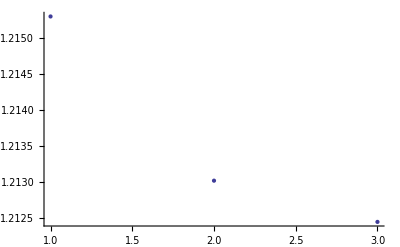

```mathematica
ListPlot[results]
```

It looks like they converge asymtotically.

```mathematica
lerr=results[[3]]-results[[2]];
```

```mathematica
beta = lambda/Eta
```

0.348598

```mathematica
CC=beta*c*hbar(*J m*)
```

1.10286×10^-26